```mathematica
h=-x^2+y^2/4-z^2/2-1;
g=x-0.1y-z;

ContourPlot3D[{h==0,g==0},{x,-10,10},{y,-10,10},{z,-10,10},MeshFunctions->{Function[{x,y,z},h-g]},MeshStyle->{{Thickness[0.01],Black}},Mesh->{{0}},ContourStyle->{Directive[Red,Opacity[0.25],Specularity[White,30]],Directive[LightBlue,Opacity[0.8]]},ImageSize->Scaled[0.8],ViewPoint->{-2.757857573706507,-0.7430621030861451,4.984183013705141},ViewVertical->{0.012636886968376546,0.7508312733328416,-0.6603731582015826}]

(*
curve=ContourPlot3D[-x^2+y^2/4-z^2/2==1,{x,-10,10},{y,-10,10},{z,-10,10}]

plane=Plot3D[x-0.1y,{x,-10,10},{y,-10,10},PlotStyle->Green]

Show[plane,curve]*)
```

-Graphics3D-

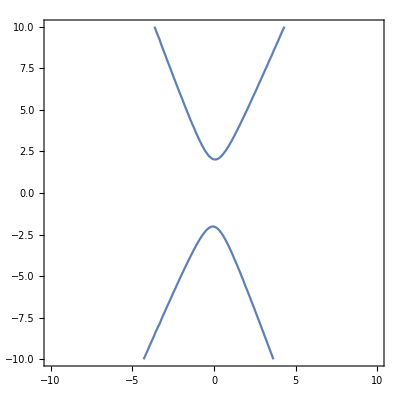

```mathematica
ContourPlot[-1.5 x^2+0.1 x y+0.245 y^2==1,{x,-10,10},{y,-10,10}]
```

```mathematica
?Perspective
```

Information::notfound: Symbol Perspective not found.

```mathematica
-Graphics3D-//Options
```

{Axes→True,AxesLabel→{None,None,None},BoxRatios→{1,1,1},DisplayFunction→Identity,FaceGridsStyle→Automatic,ImageSize→Scaled[0.8],Method→{DefaultBoundaryStyle→Directive[GrayLevel[0.3]]},PlotRange→{{-10,10},{-10,10},{-10,10}},PlotRangePadding→{Scaled[0.02],Scaled[0.02],Scaled[0.02]},Ticks→{Automatic,Automatic,Automatic},ViewPoint→{-2.75786,-0.743062,4.98418},ViewVertical→{0.0126369,0.750831,-0.660373}}